```mathematica
FullSimplify[D[-λ/(2π ϵ0)(Log[R/Sqrt[(x-R)^2+(y-R)^2]]+Log[R/Sqrt[(x+R)^2+(y+R)^2]]-Log[R/Sqrt[(x+R)^2+(y-R)^2]]-Log[R/Sqrt[(x-R)^2+(y+R)^2]]),x]]
```

-(4 R^2 y (4 R^4-3 x^4-2 x^2 y^2+y^4) λ)/(π (16 R^8+(x^2+y^2)^4+8 R^4 (x^4-6 x^2 y^2+y^4)) ϵ0)

```mathematica
FullSimplify[D[-λ/(2π ϵ0)(Log[R/Sqrt[(x-R)^2+(y-R)^2]]+Log[R/Sqrt[(x+R)^2+(y+R)^2]]-Log[R/Sqrt[(x+R)^2+(y-R)^2]]-Log[R/Sqrt[(x-R)^2+(y+R)^2]]),y]]
```

-(4 R^2 x (4 R^4+(x^2-3 y^2) (x^2+y^2)) λ)/(π (16 R^8+(x^2+y^2)^4+8 R^4 (x^4-6 x^2 y^2+y^4)) ϵ0)

```mathematica
Limit[-(4 R^2 y (4 R^4-3 x^4-2 x^2 y^2+y^4) λ)/(π (16 R^8+(x^2+y^2)^4+8 R^4 (x^4-6 x^2 y^2+y^4)) ϵ0),{x->0,y->0}]
```

0

```mathematica
Limit[-(4 R^2 x (4 R^4+(x^2-3 y^2) (x^2+y^2)) λ)/(π (16 R^8+(x^2+y^2)^4+8 R^4 (x^4-6 x^2 y^2+y^4)) ϵ0),{x->0,y->0}]
```

0

```mathematica
FullSimplify[(-(4 R^2 y (4 R^4-3 x^4-2 x^2 y^2+y^4) λ)/(π (16 R^8+(x^2+y^2)^4+8 R^4 (x^4-6 x^2 y^2+y^4)) ϵ0))/.{x->y}]
```

-(R^2 y λ)/(π R^4 ϵ0-π y^4 ϵ0)

```mathematica
FullSimplify[(-(4 R^2 x (4 R^4+(x^2-3 y^2) (x^2+y^2)) λ)/(π (16 R^8+(x^2+y^2)^4+8 R^4 (x^4-6 x^2 y^2+y^4)) ϵ0))/.{y->x}]
```

-(R^2 x λ)/(π R^4 ϵ0-π x^4 ϵ0)

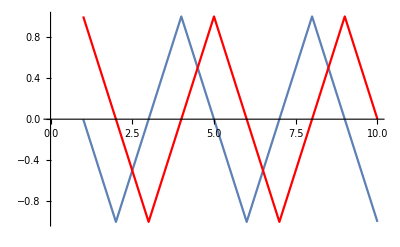

```mathematica
Show[ListLinePlot[Table[Cos[m π/2],{m,1,10}]],ListLinePlot[Table[Sin[m π/2],{m,1,10}],PlotStyle->Red]]
```

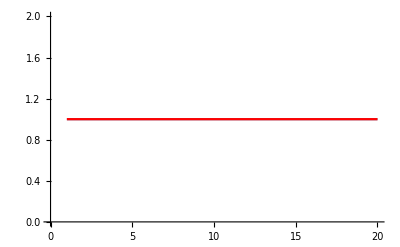

```mathematica
Show[
ListLinePlot[Table[(Cos[m π/2]^2-(-1)^m Sin[m π/2]^2),{m,1,20}]],
ListLinePlot[Table[(Cos[π/2]+Sin[π/2])^m,{m,1,20}],PlotStyle->Red]
]
```

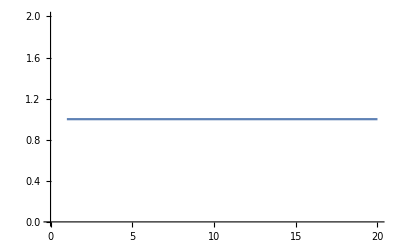

```mathematica
ListLinePlot[Table[(Cos[m π/2]^2-(-1)^m Sin[m π/2]^2),{m,1,20}]]
```

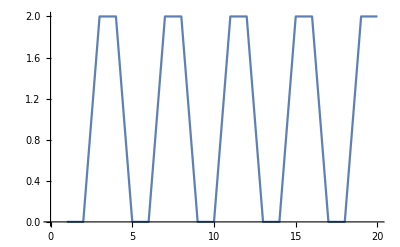

```mathematica
ListLinePlot[Table[(Cos[π/2]+Sin[π/2])^m+(-1)^m(Cos[m π/2]+Sin[m π/2]),{m,1,20}]]
```

```mathematica
Manipulate[Plot[(Cos[θ]+Sin[θ])^m-Cos[m π/2]Cos[m θ]- Sin[m π/2]Sin[m θ],{θ,0,π/2}],{m,1,10,1}]
```

```mathematica
FullSimplify[D[-Log[((x-R)^2+(y+R)^2)((x+R)^2+(y-R)^2)/((x+R)^2+(y+R)^2)/((x-R)^2+(y-R)^2)],x]]
```

-(16 R^2 y (4 R^4-3 x^4-2 x^2 y^2+y^4))/(16 R^8+(x^2+y^2)^4+8 R^4 (x^4-6 x^2 y^2+y^4))

```mathematica
FullSimplify[D[-Log[((x-R)^2+(y+R)^2)((x+R)^2+(y-R)^2)/((x+R)^2+(y+R)^2)/((x-R)^2+(y-R)^2)],y]]
```

-(16 R^2 x (4 R^4+(x^2-3 y^2) (x^2+y^2)))/(16 R^8+(x^2+y^2)^4+8 R^4 (x^4-6 x^2 y^2+y^4))

```mathematica
FullSimplify[(-(16 R^2 y (4 R^4-3 x^4-2 x^2 y^2+y^4))/(16 R^8+(x^2+y^2)^4+8 R^4 (x^4-6 x^2 y^2+y^4)))/.{x->r Cos[θ],y-> r Sin[θ]}]
```

(16 (-4 r R^6 Sin[θ]+r^5 R^2 Sin[3 θ]))/(r^8+16 R^8+8 r^4 R^4 Cos[4 θ])

```mathematica
FullSimplify[(-(16 R^2 x (4 R^4+(x^2-3 y^2) (x^2+y^2)))/(16 R^8+(x^2+y^2)^4+8 R^4 (x^4-6 x^2 y^2+y^4)))/.{x->r Cos[θ],y-> r Sin[θ]}]
```

-(16 (4 r R^6 Cos[θ]+r^5 R^2 Cos[3 θ]))/(r^8+16 R^8+8 r^4 R^4 Cos[4 θ])

```mathematica
Series[(16 (-4 r R^6 Sin[θ]+r^5 R^2 Sin[3 θ]))/(r^8+16 R^8+8 r^4 R^4 Cos[4 θ]),{r,0,2}]
```

-(4 Sin[θ] r)/R^2+O[r]^3

```mathematica
Series[-(16 (4 r R^6 Cos[θ]+r^5 R^2 Cos[3 θ]))/(r^8+16 R^8+8 r^4 R^4 Cos[4 θ]),{r,0,2}]
```

-(4 Cos[θ] r)/R^2+O[r]^3

```mathematica
D[-λ/(2π ϵ0)Log[R/Sqrt[(x-R)^2+y^2]],x]
```

((-R+x) λ)/(2 π ((-R+x)^2+y^2) ϵ0)

```mathematica
D[-λ/(2π ϵ0)Log[R/Sqrt[(x-R)^2+y^2]],y]
```

(y λ)/(2 π ((-R+x)^2+y^2) ϵ0)